```mathematica
SetDirectory["C:\\Users\\physk\\OneDrive\\Desktop\\Non-Markovian System eta Data\\eta_0_beta_vary_omega_2"];
LNDatabeta005=ReadList["LNData_NM_beta_0.05.txt"];
LNDatabeta010=ReadList["LNData_NM_beta_0.1.txt"];
LNDatabeta015=ReadList["LNData_NM_beta_0.15.txt"];
LNDatabeta020=ReadList["LNData_NM_beta_0.2.txt"];
LNDatabeta025=ReadList["LNData_NM_beta_0.25.txt"];
LNDatabeta030=ReadList["LNData_NM_beta_0.3.txt"];
LNDatabeta035=ReadList["LNData_NM_beta_0.35.txt"];
LNDatabeta040=ReadList["LNData_NM_beta_0.4.txt"];
LNDatabeta045=ReadList["LNData_NM_beta_0.45.txt"];
LNDatabeta050=ReadList["LNData_NM_beta_0.5.txt"];
LNDatabeta055=ReadList["LNData_NM_beta_0.55.txt"];
LNDatabeta060=ReadList["LNData_NM_beta_0.6.txt"];
LNDatabeta065=ReadList["LNData_NM_beta_0.65.txt"];
LNDatabeta070=ReadList["LNData_NM_beta_0.7.txt"];
LNDatabeta075=ReadList["LNData_NM_beta_0.75.txt"];
LNDatabeta100=ReadList["LNData_NM_beta_1.txt"];
LNDatabeta125=ReadList["LNData_NM_beta_1.25.txt"];
LNDatabeta150=ReadList["LNData_NM_beta_1.5.txt"];
LNDatabeta175=ReadList["LNData_NM_beta_1.75.txt"];
LNDatabeta200=ReadList["LNData_NM_beta_2.txt"];
```

```mathematica
MeanBetaData={
{0.05, Mean[Table[LNDatabeta005[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.10, Mean[Table[LNDatabeta010[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.15, Mean[Table[LNDatabeta015[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.20, Mean[Table[LNDatabeta020[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.25, Mean[Table[LNDatabeta025[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.30, Mean[Table[LNDatabeta030[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.35, Mean[Table[LNDatabeta035[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.40, Mean[Table[LNDatabeta040[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.45, Mean[Table[LNDatabeta045[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.50, Mean[Table[LNDatabeta050[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.55, Mean[Table[LNDatabeta055[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.60, Mean[Table[LNDatabeta060[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.65, Mean[Table[LNDatabeta065[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.70, Mean[Table[LNDatabeta070[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.75, Mean[Table[LNDatabeta075[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{1, Mean[Table[LNDatabeta100[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{1.25, Mean[Table[LNDatabeta125[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{1.5, Mean[Table[LNDatabeta150[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{1.75, Mean[Table[LNDatabeta175[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{2, Mean[Table[LNDatabeta200[[1]][[pt]][[2]], {pt, 100, 1001}]]}};

(* LN12 and LN34 Data *)
LNBetaData={
{LNDatabeta005[[1]], LNDatabeta005[[6]], 0.05},
{LNDatabeta010[[1]], LNDatabeta010[[6]], 0.10},
{LNDatabeta015[[1]], LNDatabeta015[[6]], 0.15},
{LNDatabeta020[[1]], LNDatabeta020[[6]], 0.20},
{LNDatabeta025[[1]], LNDatabeta025[[6]], 0.25},
{LNDatabeta030[[1]], LNDatabeta030[[6]], 0.30},
{LNDatabeta035[[1]], LNDatabeta035[[6]], 0.35},
{LNDatabeta040[[1]], LNDatabeta040[[6]], 0.40},
{LNDatabeta045[[1]], LNDatabeta045[[6]], 0.45},
{LNDatabeta050[[1]], LNDatabeta050[[6]], 0.50},
{LNDatabeta055[[1]], LNDatabeta055[[6]], 0.55},
{LNDatabeta060[[1]], LNDatabeta060[[6]], 0.60},
{LNDatabeta065[[1]], LNDatabeta065[[6]], 0.65},
{LNDatabeta070[[1]], LNDatabeta070[[6]], 0.70},
{LNDatabeta075[[1]], LNDatabeta075[[6]], 0.75},
{LNDatabeta100[[1]], LNDatabeta100[[6]], 1.00},
{LNDatabeta125[[1]], LNDatabeta125[[6]], 1.25},
{LNDatabeta150[[1]], LNDatabeta150[[6]], 1.50},
{LNDatabeta175[[1]], LNDatabeta175[[6]], 1.75},
{LNDatabeta200[[1]], LNDatabeta200[[6]], 2.00}};
```

```mathematica
(* Plotting Properties *)
width=600;
height=300;
PlotFormat1={LabelStyle->Directive[18], BaseStyle->"Latin Modern Roman", ImageSize->{UpTo[width], UpTo[height]}, AspectRatio->height/width};
LabelingInfo1={AxesLabel->{"β", "Saturated ℒ𝒩_12"}, PlotLabel->"n=4, β, η=0, m=1, ω=2, Ω=2, γ=0.5"};
LabelingInfo2={AxesLabel->{"τ", "𝒩"}};
```

```mathematica
(* LN12 and LN34 Plot as a function of β *)
LNBetaPlots=Table[ListPlot[{LNBetaData[[betavalue]][[1]], LNBetaData[[betavalue]][[2]]}, Joined->True, Evaluate[PlotFormat1], Evaluate[LabelingInfo2], PlotLabel->"n=4, β="<>ToString[LNBetaData[[betavalue]][[3]]]<>", η=0, m=1, ω=2, Ω=2, γ=0.5}"], {betavalue, 1, Length[LNBetaData]}];
ListAnimate[LNBetaPlots, AnimationRunning->False, ControlPlacement->Bottom]
```

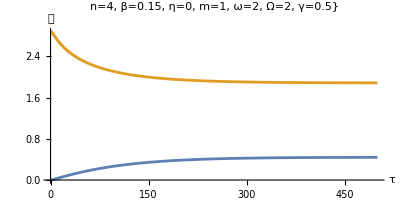
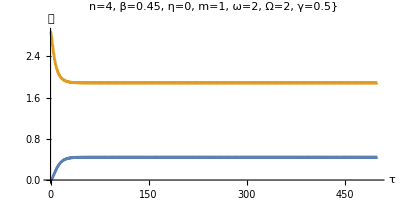

```mathematica
Row[{LNBetaPlots[[3]],LNBetaPlots[[9]]}]
```

```mathematica
(* Plotting Properties *)
width=400;
height=400;
PlotFormat2={LabelStyle->Directive[18, Black], BaseStyle->"Latin Modern Roman", ImageSize->{UpTo[width], UpTo[height]}, AspectRatio->height/width};
FindingBetaOptimumOmega2=Rasterize[ListLinePlot[{LNBetaData[[9]][[1]], LNBetaData[[9]][[2]], LNBetaData[[3]][[1]], LNBetaData[[3]][[2]]}, Evaluate[PlotFormat2], Evaluate[LabelingInfo2], PlotStyle->{Directive[Darker[Blue], Thickness[0.0025]],Directive[Darker[Red], Thickness[0.0025]], Directive[Blue, Dashed],Directive[Red, Dashed]}]]
```

-Graphics-

```mathematica
SetDirectory["C:\\Users\\physk\\OneDrive\\Desktop"]
Export["FindingBetaOptimumOmega2.png", FindingBetaOptimumOmega2]
```

C:\Users\physk\OneDrive\Desktop

FindingBetaOptimumOmega2.png

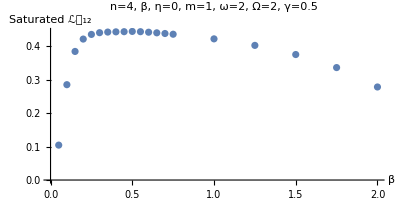
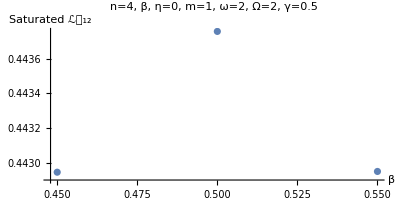

```mathematica
(* Points *)
MeanBetaDataptPlot=ListPlot[Table[MeanBetaData[[betavalue]], {betavalue, 1, Length[MeanBetaData]}], Joined->False, Evaluate[PlotFormat1], Evaluate[LabelingInfo1]];
(* Plot only Points of where suspected Max is *)
MeanBetaDataptPlotZoom=ListPlot[MeanBetaData[[9;;11]], Joined->False, Evaluate[PlotFormat1], Evaluate[LabelingInfo1]];
(* Show Side by Side *)
Row[{MeanBetaDataptPlot, MeanBetaDataptPlotZoom}]
```

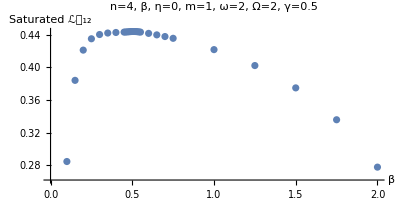
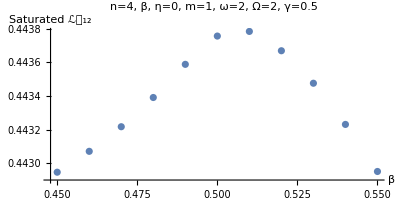

```mathematica
(* Load Detailed Data around suspected Maximum point *)
LNDatabeta045=ReadList["LNData_NM_beta_0.45.txt"];
LNDatabeta046=ReadList["LNData_NM_beta_0.46.txt"];
LNDatabeta047=ReadList["LNData_NM_beta_0.47.txt"];
LNDatabeta048=ReadList["LNData_NM_beta_0.48.txt"];
LNDatabeta049=ReadList["LNData_NM_beta_0.49.txt"];
LNDatabeta050=ReadList["LNData_NM_beta_0.5.txt"];
LNDatabeta051=ReadList["LNData_NM_beta_0.51.txt"];
LNDatabeta052=ReadList["LNData_NM_beta_0.52.txt"];
LNDatabeta053=ReadList["LNData_NM_beta_0.53.txt"];
LNDatabeta054=ReadList["LNData_NM_beta_0.54.txt"];
LNDatabeta055=ReadList["LNData_NM_beta_0.55.txt"];

(* Reassign MeanBetaData *)
MeanBetaData={
{0.05, Mean[Table[LNDatabeta005[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.10, Mean[Table[LNDatabeta010[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.15, Mean[Table[LNDatabeta015[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.20, Mean[Table[LNDatabeta020[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.25, Mean[Table[LNDatabeta025[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.30, Mean[Table[LNDatabeta030[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.35, Mean[Table[LNDatabeta035[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.40, Mean[Table[LNDatabeta040[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.45, Mean[Table[LNDatabeta045[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.46, Mean[Table[LNDatabeta046[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.47, Mean[Table[LNDatabeta047[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.48, Mean[Table[LNDatabeta048[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.49, Mean[Table[LNDatabeta049[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.50, Mean[Table[LNDatabeta050[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.51, Mean[Table[LNDatabeta051[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.52, Mean[Table[LNDatabeta052[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.53, Mean[Table[LNDatabeta053[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.54, Mean[Table[LNDatabeta054[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.55, Mean[Table[LNDatabeta055[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.60, Mean[Table[LNDatabeta060[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.65, Mean[Table[LNDatabeta065[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.70, Mean[Table[LNDatabeta070[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{0.75, Mean[Table[LNDatabeta075[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{1, Mean[Table[LNDatabeta100[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{1.25, Mean[Table[LNDatabeta125[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{1.5, Mean[Table[LNDatabeta150[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{1.75, Mean[Table[LNDatabeta175[[1]][[pt]][[2]], {pt, 100, 1001}]]},
{2, Mean[Table[LNDatabeta200[[1]][[pt]][[2]], {pt, 100, 1001}]]}};

(* Points *)
MeanBetaDataptPlot=ListPlot[Table[MeanBetaData[[betavalue]], {betavalue, 1, Length[MeanBetaData]}], Joined->False, Evaluate[PlotFormat1], Evaluate[LabelingInfo1]];
(* Plot only Points of where suspected Max is *)
MeanBetaDataptPlotZoom=ListPlot[MeanBetaData[[9;;19]], Joined->False, Evaluate[PlotFormat1], Evaluate[LabelingInfo1]];
(* Show Side by Side *)
Row[{MeanBetaDataptPlot, MeanBetaDataptPlotZoom}]
```

InterpolatingFunction[…]

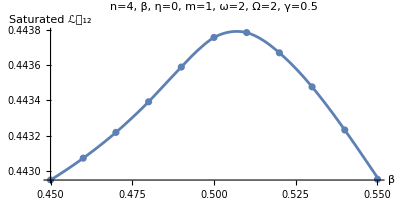

```mathematica
(* Interpolation: Must zoom in to where the suspected maximum is. *)
iMeanBetafunc=Interpolation[MeanBetaData[[9;;18]]]
iMeanBetaDatalinePlot=Plot[iMeanBetafunc[x], {x, 0.45, 0.55}, Evaluate[PlotFormat1], Evaluate[LabelingInfo1]];
(* Show together *)
Show[iMeanBetaDatalinePlot, MeanBetaDataptPlotZoom]
```

```mathematica
(* Take the derivative of the Interpolation Function *)
derivfunc[β_]:=D[iMeanBetafunc[x], x]/.x->β
```

```mathematica
(* Calculating the value of the derivative of Interpolation Function near the maximum. Get start and end values from the graph. *)
start= 0.506947;
end=0.506956;
deridata=Table[{β, derivfunc[β]}, {β, start, end, 10^-6}];

(* Finding Optimum β for when Ω=ω=2 *)
βmax={};
Table[If[deridata[[value]][[2]]>0 && deridata[[value+1]][[2]]<0, AppendTo[βmax, Mean[{deridata[[value]][[1]],deridata[[value+1]][[1]]}]]], {value, 1, Length[deridata]-1}];
optimumpt=Flatten[{βmax, iMeanBetafunc[βmax]}]
```

{0.506955,0.44379}

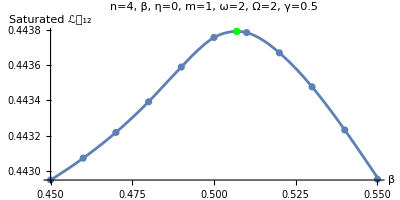

```mathematica
optimumptPlot=ListPlot[{optimumpt}, Joined->False, Evaluate[PlotFormat1], Evaluate[LabelingInfo1], PlotStyle->Green];
Show[iMeanBetaDatalinePlot, MeanBetaDataptPlotZoom, optimumptPlot]
```